```mathematica
Nt = 455(*551*) ;(*151*)
ti = 0; tf =5(*1*); 
deltat = (tf - ti) /Nt ;
Nx = 455(*551*); (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = -40; xf = 40;
deltax = (xf - xi) / Nx;
c = 1;(*speed of 10 worked*)
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.0625

```mathematica
deltax//N
```

0.175824

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
X = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

(*X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];*)

(*deltax = X[[2]] - X[[1]];
deltat = T[[2]] - T[[1]];*)

f[x_] = ⅇ^(- (x)^2);
(*f[x_] = ⅇ^(- (x)^2);
f[x_] = ⅇ^(- ((x-xi)*((2*Pi))/(xf-xi))^2);*)

fexact[t_,x_] = ⅇ^(- ((x-(c*t)))^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
(*fexact[t_,x_] = ⅇ^(- ((((x-xi)*((2*Pi))/(xf-xi))-t))^2)*)
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[((2*Pi)/(xf - xi))*Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*LD6*)
ULD6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD6[[1,All]] = N[f[X],32];
ULD6 = Chop[ULD6, 10^(-307)];
ULD6 = Developer`ToPackedArray[ULD6, Real]; 
Developer`PackedArrayQ[ULD6]


ILD6 = N[IdentityMatrix[Length[D1]],32];
ALD6 = N[ILD6 - ((DL / 2)) + (((MatrixPower[DL,2])/10)) - (((MatrixPower[DL,3])/120)),32];
BLD6 = N[ILD6 + ((DL / 2)) + (((MatrixPower[DL,2])/10)) + (((MatrixPower[DL,3])/120)),32];
MLD6 = N[Inverse[ALD6].BLD6,32];
EMLD6 = N[MLD6 - ILD6,32];

EMLD6= Developer`ToPackedArray[EMLD6, Real]; 

Do[ULD6[[n+1,All]] = ULD6[[n,All]] + (EMLD6).ULD6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK6*)
URK6= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK6[[1,All]] = N[f[X],32];
URK6 = Chop[URK6, 10^(-307)];
URK6 = Developer`ToPackedArray[URK6, Real]; 
Developer`PackedArrayQ[URK6]

IRK6 = N[IdentityMatrix[Length[DL]],32];


MRK6 = N[IRK6 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])) + ((1/120) * (MatrixPower[DL,5])) + ((1/720) * (MatrixPower[DL,6])),32];

EMRK6 = N[MRK6 - IRK6,32];

EMRK6= Developer`ToPackedArray[EMRK6, Real]; 

Do[URK6[[n+1,All]] = URK6[[n,All]] + (EMRK6).URK6[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD8*)
ULD8= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD8[[1,All]] = N[f[X],32];
ULD8 = Chop[ULD8, 10^(-307)];
ULD8 = Developer`ToPackedArray[ULD8, Real]; 
Developer`PackedArrayQ[ULD8]


ILD8 = N[IdentityMatrix[Length[D1]],32];
ALD8 = N[ILD8 - ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) - (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
BLD8 = N[ILD8 + ((DL / 2)) + (((3*MatrixPower[DL,2])/28)) + (((MatrixPower[DL,3])/84)) + (((MatrixPower[DL,4])/1680)),32];
MLD8 = N[Inverse[ALD8].BLD8,32];
EMLD8 = N[MLD8 - ILD8,32];

EMLD8= Developer`ToPackedArray[EMLD8, Real]; 

Do[ULD8[[n+1,All]] = ULD8[[n,All]] + (EMLD8).ULD8[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*Now we don't need D1 or DL to have 32 digit accuracy so can put it into a packed array*)
D1 = Developer`ToPackedArray[D1, Real];
DL = Developer`ToPackedArray[DL, Real];
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
(*RK6*)
abserrRK6 = Abs[URK6-Uexact];
errorRK6 = Table[0,{i,1,Length[abserrRK6]}];
errorRK6 = Developer`ToPackedArray[errorRK6, Real];
Do[
errorRK6[[i]] = Norm[abserrRK6[[i,All]], 1] * deltax;
,{i,1,Length[errorRK6]}
];
```

```mathematica
(*LD6*)
abserrLD6 = Abs[ULD6-Uexact];
errorLD6 = Table[0,{i,1,Length[abserrLD6]}];
errorLD6 = Developer`ToPackedArray[errorLD6, Real];
Do[
errorLD6[[i]] = Norm[abserrLD6[[i,All]], 1] * deltax;
,{i,1,Length[errorLD6]}
];
```

```mathematica
(*LD8*)
abserrLD8 = Abs[ULD8-Uexact];
errorLD8 = Table[0,{i,1,Length[abserrLD8]}];
errorLD8 = Developer`ToPackedArray[errorLD8, Real];
Do[
errorLD8[[i]] = Norm[abserrLD8[[i,All]], 1] * deltax;
,{i,1,Length[errorLD8]}
];
```

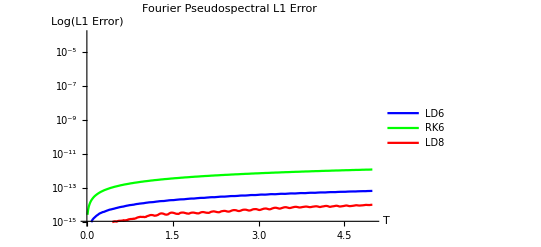

```mathematica
ListLogPlot[{Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue,Green,Red},PlotLegends->{"LD6","RK6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

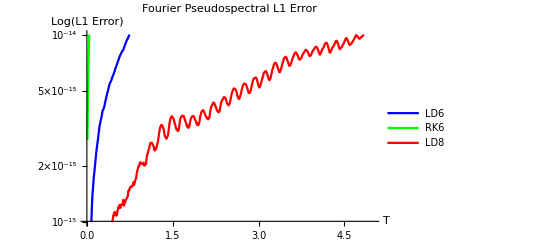

```mathematica
ListLogPlot[{Transpose[{T,errorLD6}],Transpose[{T,errorRK6}],Transpose[{T,errorLD8}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-14}}, PlotStyle->{Blue,Green,Red},PlotLegends->{"LD6","RK6","LD8"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4,errorLD6,errorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,ULD6[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{xi,xf},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,(ULD6[[n]] - Uexact[[n]])}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```